# CRNSSA Demo

```mathematica
<<CRNSSA`;
?CRNSSA`*
```

## Reaction System 0: f(x) = 1

```mathematica
rxnsys0 = {
rxnl[{x},{y},1],
rxnl[{y,y},{y},1],
conc[{x, y},5]
};
SpeciesInRxnsys[rxnsys0]
```

{x,y}

{{{5,5},{5,4},{4,5},{4,4},{4,3},{3,4},{2,5},{1,6},{1,5},{0,6},{0,5},{0,4},{0,3},{0,2},{0,1}},{0.,0.0372411,0.079479,0.128857,0.252285,0.466933,0.575846,0.581333,0.588102,0.849553,0.860843,0.892686,0.966132,1.28055,1.97484}}

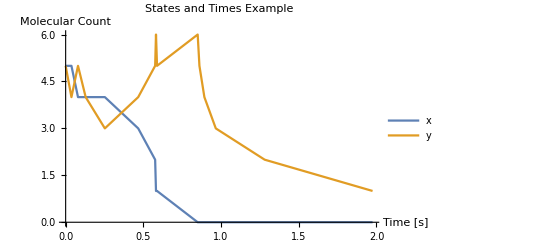

```mathematica
SimulateDirectSSA[rxnsys0,outputTS->False]
PlotLastSimulation[PlotLabel->"States and Times Example"]
```

{{5,5},{5,4},{4,5},{4,4},{3,5},{3,4},{3,3},{3,2},{2,3},{2,2},{1,3},{0,4},{0,3},{0,2},{0,1}}

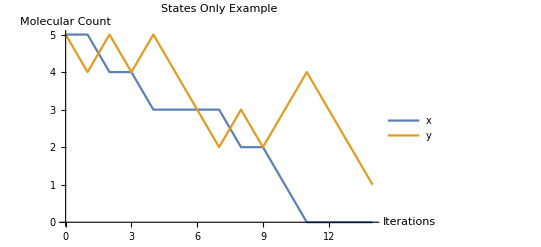

```mathematica
SimulateDirectSSA[rxnsys0,statesOnly->True,outputTS->False]
PlotLastSimulation[PlotLabel->"States Only Example"]
```

## Reaction System 1: Demonstrating functionality

```mathematica
rxnsys1={
rxn[0,2x+3y+8z[j-k][j+k],3],
revrxn[z[j+k][j-k],1,4,5],
rxnl[{},{z[j+k][j-k],z[j-k][j+k],x,x},10],
conc[a, 10],
conc[{a,b,x,y},1000]
}
SpeciesInRxnsys[rxnsys1]
```

{0 →^3 2 x+3 y+8 z[j-k][j+k] ,z[j+k][j-k] ⇄_5^4 1 ,rxnl[{},{z[j+k][j-k],z[j-k][j+k],x,x},10],conc[a,10],conc[{a,b,x,y},1000]}

{a,b,x,y,z[j-k][j+k],z[j+k][j-k]}

```mathematica
SpeciesInRxnsys[rxnsys1, z[_][_]]
```

{z[j-k][j+k],z[j+k][j-k]}

```mathematica
SimulateDirectSSA[rxnsys1,iterEnd->15,useIter->True,statesOnly->True,outputTS->False]
```

{{1010,1000,1000,1000,0,0},{1010,1000,1002,1003,8,0},{1010,1000,1002,1003,8,1},{1010,1000,1002,1003,8,0},{1010,1000,1002,1003,8,1},{1010,1000,1004,1006,16,1},{1010,1000,1006,1009,24,1},{1010,1000,1006,1009,24,2},{1010,1000,1006,1009,24,3},{1010,1000,1006,1009,24,2},{1010,1000,1006,1009,24,3},{1010,1000,1008,1012,32,3},{1010,1000,1008,1012,32,2},{1010,1000,1008,1012,32,1},{1010,1000,1010,1012,33,2},{1010,1000,1012,1012,34,3}}

```mathematica
SimulateDirectSSA[rxnsys1,iterEnd->15,useIter->True,finalOnly->True,outputTS->False]
```

{{{1010,1000,1018,1003,16,4}},{0.343183}}

## Reaction System 2: A deterministic CRN

```mathematica
rxnsys2={
rxn[x1,y+z1,2],
rxn[x2,y+z2,2],
rxn[z1+z2,k,1],
rxn[k+y,1,3],
conc[x1,5],
conc[x2,15]
}
SpeciesInRxnsys[rxnsys2]
```

{x1 →^2 y+z1 ,x2 →^2 y+z2 ,z1+z2 →^1 k ,k+y →^3 1 ,conc[x1,5],conc[x2,15]}

{k,x1,x2,y,z1,z2}

TimeSeries[…]

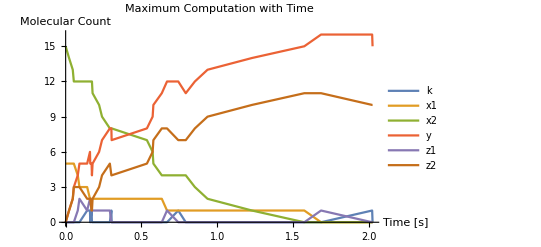

```mathematica
SimulateDirectSSA[rxnsys2]
PlotLastSimulation[PlotLabel->"Maximum Computation with Time"]
```

TimeSeries[…]

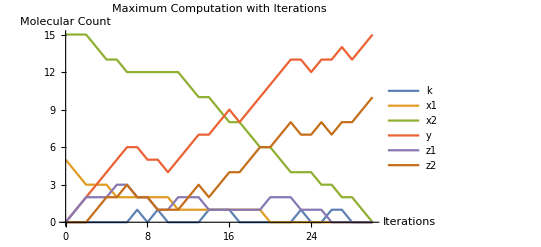

```mathematica
SimulateDirectSSA[rxnsys2,statesOnly->True]
PlotLastSimulation[PlotLabel->"Maximum Computation with Iterations"]
```

```mathematica
SimulateDirectSSA[rxnsys2,statesOnly->True,finalOnly->True,outputTS->False]
SpeciesInRxnsys[rxnsys2]
```

{{0,0,0,15,0,10}}

{k,x1,x2,y,z1,z2}

## Reaction System 3: Demonstrating erroneous input handling

```mathematica
rxnsys3={
rxn[a,b,1],
rxn[c,d,2,3],
rxxn[e,f,4],
reaction[g,h,5],
revrxn[i,j,6,7],
revrxn[k,l,8],
rxnl[{m},{},9],
rxnl[o,p,10],
conc[10],
conc[{a,b,c,d, e, f, g, h},20],
concs[{i, j, k, l, m, o , p},30]
}
SpeciesInRxnsys[rxnsys3]
```

{a →^1 b ,rxn[c,d,2,3],rxxn[e,f,4],reaction[g,h,5],i ⇄_7^6 j ,revrxn[k,l,8],rxnl[{m},{},9],rxnl[o,p,10],conc[10],conc[{a,b,c,d,e,f,g,h},20],concs[{i,j,k,l,m,o,p},30]}

RxnsysToOdesys::rxnargs: rxn[c,d,2,3] is invalid as 3 arguments are expected

RxnsysToOdesys::revrxnargs: revrxn[k,l,8] is invalid as 4 arguments are expected

RxnsysToOdesys::concargs: conc[10] is invalid as 2 arguments are expected

RxnsysToOdesys::rxnllists: rxnl[o,p,10] is invalid as lists are expected for the first and second arguments

$Aborted

```mathematica
SimulateDirectSSA[rxnsys3,iterEnd->0.5,useIter->True,finalOnly->True]
PlotLastSimulation[]
```

$Aborted

PlotLastSimulation::finalonlyerr: Error: Cannot plot when finalOnly = True